```mathematica
AppendTo[$Path,NotebookDirectory[]<>"../src"];
<<affine.m;
```

```mathematica
tt1=Table[freudenthalMultiplicities[Subscript[B, 2]][weight[Subscript[B, 2]][i,i]]//Timing,{i,10}];
tt2=Table[racahMultiplicities[Subscript[B, 2]][weight[Subscript[B, 2]][i,i]]//Timing,{i,10}];
```

```mathematica
Table[freudenthalMultiplicities[Subscript[B, 2]][weight[Subscript[B, 2]][i,i]]//Timing,{i,10}]
```

{{0.040003,mults$1929},{0.108006,mults$1931},{0.192012,mults$1933},{0.62804,mults$1935},{0.936058,mults$1937},{2.36415,mults$1939},{3.33221,mults$1941},{6.89243,mults$1943},{8.49253,mults$1945},{14.7049,mults$1947}}

```mathematica
Table[racahMultiplicities[Subscript[B, 2]][weight[Subscript[B, 2]][i,i]]//Timing,{i,10}]
```

{{0.044003,mults$1950},{0.128008,mults$1952},{0.104007,mults$1954},{0.304019,mults$1956},{0.424026,mults$1958},{0.848053,mults$1960},{1.03607,mults$1962},{1.73611,mults$1964},{2.13213,mults$1966},{3.1842,mults$1968}}

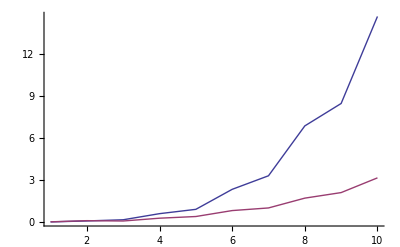

```mathematica
ListPlot[{#[[1]]&/@Out[23],#[[1]]&/@Out[24]},Joined-> True]
```

```mathematica
Export["timing.pdf",ListPlot[{#[[1]]&/@tt1,#[[1]]&/@tt2},Joined-> True]]
```

timing.pdf

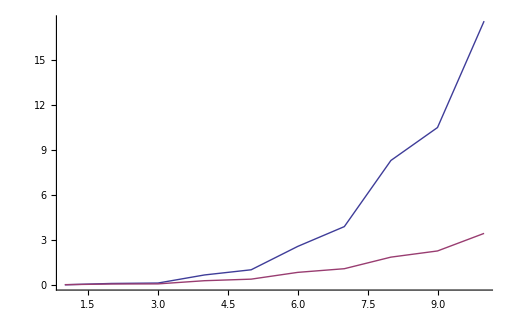

```mathematica
b2=regularSubalgebra[Subscript[B, 4]][3,4]
```

finiteRootSystem[2,4,{finiteWeight[4,{0,0,1,-1}],finiteWeight[4,{0,0,0,1}]}]

```mathematica
brc=simpleBranching[Subscript[B, 4],b2][weight[Subscript[B, 4]][2,2,2,2]]//Timing
```

$Aborted

```mathematica
freudenthalMultiplicities[Subscript[B, 4]][weight[Subscript[B, 4]][2,2,2,2]]//Timing
```

$Aborted

```mathematica
dimension[Subscript[B, 4]][weight[Subscript[B, 4]][2,2,2,2]]
```

43046721